```mathematica
<<Quaternions`
```

```mathematica
Wa=Quaternion[a1,a2,a3,a4];
X0=Quaternion[x01,x02,x03,x04];
NRefImu=Quaternion[a1,a2,a3,a4];
X1=Quaternion[x11,x12,x13,x14];

Wc=Quaternion[c1,c2,c3,c4];
n=Quaternion[n1,n2,n3,n4];
T=Quaternion[t1,t2,t3,t4];
NArmImu=Quaternion[b1,b2,b3,b4];
```

```mathematica
{a1,a2,a3,a4} ={0.618,0.315,0.303,0.654}; Subscript[W, A];
{x01,x02,x03,x04} ;
{c1,c2,c3,c4} = {-0.6,-0.04,-0.026,0.745}; A^n;
{x11,x12,x13,x14};
{a1,a2,a3,a4} ={0.95,0.,0.25,0.};Subscript[W, c]
{a1,a2,a3,a4} ={0.004,0.01,0.974,0.228};n
{c1,c2,c3,c4} = {-0.7,-0.69,0.138,0.032};T
{a1,a2,a3,a4} ={-0.02,0.028,0.45,0.892}; T^n;
```

W_c

Quaternion[n1,n2,n3,n4]

Quaternion[t1,t2,t3,t4]

```mathematica
A=Quaternion[0.618,0.315,0.303,0.654];
{a1,a2,a3,a4} ={0.95,0.,0.25,0.}; n;
{c1,c2,c3,c4} = {-0.6,-0.04,-0.026,0.745}; Z;
{a1,a2,a3,a4} ={-0.02,0.028,0.45,0.892}; T^n;
{a1,a2,a3,a4} ={0.004,0.01,0.974,0.228};Z^n;

{c1,c2,c3,c4} = {-0.7,-0.69,0.138,0.032};T;
```

Quaternion[0.618,0.315,0.303,0.654]

```mathematica
{0.95,0.,0.25,0.}
NRefImu**(NArmImu**Wc)
```

{0.95,0.,0.25,0.}

Quaternion[-a4 (b4 c1-b3 c2+b2 c3+b1 c4)-a3 (b3 c1+b4 c2+b1 c3-b2 c4)-a2 (b2 c1+b1 c2-b4 c3+b3 c4)+a1 (b1 c1-b2 c2-b3 c3-b4 c4),a3 (b4 c1-b3 c2+b2 c3+b1 c4)-a4 (b3 c1+b4 c2+b1 c3-b2 c4)+a1 (b2 c1+b1 c2-b4 c3+b3 c4)+a2 (b1 c1-b2 c2-b3 c3-b4 c4),-a2 (b4 c1-b3 c2+b2 c3+b1 c4)+a1 (b3 c1+b4 c2+b1 c3-b2 c4)+a4 (b2 c1+b1 c2-b4 c3+b3 c4)+a3 (b1 c1-b2 c2-b3 c3-b4 c4),a1 (b4 c1-b3 c2+b2 c3+b1 c4)+a2 (b3 c1+b4 c2+b1 c3-b2 c4)-a3 (b2 c1+b1 c2-b4 c3+b3 c4)+a4 (b1 c1-b2 c2-b3 c3-b4 c4)]

```mathematica
{x01,x02,x03,x04} ** {a1,a2,a3,a4}
```

{x01,x02,x03,x04}**{a1,a2,a3,a4}

```mathematica
Solve[
{(a1 b1-a2 b2-a3 b3-a4 b4) x01-(a2 b1+a1 b2-a4 b3+a3 b4) x02-(a3 b1+a4 b2+a1 b3-a2 b4) x03-(a4 b1-a3 b2+a2 b3+a1 b4) x04== c1,
(a2 b1+a1 b2-a4 b3+a3 b4) x01+(a1 b1-a2 b2-a3 b3-a4 b4) x02+(a4 b1-a3 b2+a2 b3+a1 b4) x03-(a3 b1+a4 b2+a1 b3-a2 b4) x04 == c2,
(a3 b1+a4 b2+a1 b3-a2 b4) x01-(a4 b1-a3 b2+a2 b3+a1 b4) x02+(a1 b1-a2 b2-a3 b3-a4 b4) x03+(a2 b1+a1 b2-a4 b3+a3 b4) x04 == c3,
(a4 b1-a3 b2+a2 b3+a1 b4) x01+(a3 b1+a4 b2+a1 b3-a2 b4) x02-(a2 b1+a1 b2-a4 b3+a3 b4) x03+(a1 b1-a2 b2-a3 b3-a4 b4) x04 == c4},{x01,x02,x03,x04}
] // Simplify
```

{{x01→(-a3 b3 c1-a4 b4 c1-a4 b3 c2+a3 b4 c2+a3 b1 c3+a4 b2 c3+a4 b1 c4-a3 b2 c4+a2 (-b2 c1+b1 c2-b4 c3+b3 c4)+a1 (b1 c1+b2 c2+b3 c3+b4 c4))/((a1^2+a2^2+a3^2+a4^2) (b1^2+b2^2+b3^2+b4^2)),x02→(a4 b3 c1-a3 b4 c1-a3 b3 c2-a4 b4 c2-a4 b1 c3+a3 b2 c3+a3 b1 c4+a4 b2 c4+a1 (-b2 c1+b1 c2-b4 c3+b3 c4)-a2 (b1 c1+b2 c2+b3 c3+b4 c4))/((a1^2+a2^2+a3^2+a4^2) (b1^2+b2^2+b3^2+b4^2)),x03→(-a1 b3 c1+a2 b4 c1+a2 b3 c2+a1 b4 c2+a1 b1 c3-a2 b2 c3-a2 b1 c4-a1 b2 c4+a4 (-b2 c1+b1 c2-b4 c3+b3 c4)-a3 (b1 c1+b2 c2+b3 c3+b4 c4))/((a1^2+a2^2+a3^2+a4^2) (b1^2+b2^2+b3^2+b4^2)),x04→(-a2 b3 c1-a1 b4 c1-a1 b3 c2+a2 b4 c2+a2 b1 c3+a1 b2 c3+a1 b1 c4-a2 b2 c4+a3 (b2 c1-b1 c2+b4 c3-b3 c4)-a4 (b1 c1+b2 c2+b3 c3+b4 c4))/((a1^2+a2^2+a3^2+a4^2) (b1^2+b2^2+b3^2+b4^2))}}

```mathematica
{{c1->a1b1x01-a2b2x01-a3b3x01-a4b4x01-a2b1x02-a1b2x02+a4b3x02-a3b4x02-a3b1x03-a4b2x03-a1b3x03+a2b4x03-a4b1x04+a3b2x04-a2b3x04-a1b4x04,c2->a2b1x01+a1b2x01-a4b3x01+a3b4x01+a1b1x02-a2b2x02-a3b3x02-a4b4x02+a4b1x03-a3b2x03+a2b3x03+a1b4x03-a3b1x04-a4b2x04-a1b3x04+a2b4x04,c3->a3b1x01+a4b2x01+a1b3x01-a2b4x01-a4b1x02+a3b2x02-a2b3x02-a1b4x02+a1b1x03-a2b2x03-a3b3x03-a4b4x03+a2b1x04+a1b2x04-a4b3x04+a3b4x04,c4->a4b1x01-a3b2x01+a2b3x01+a1b4x01+a3b1x02+a4b2x02+a1b3x02-a2b4x02-a2b1x03-a1b2x03+a4b3x03-a3b4x03+a1b1x04-a2b2x04-a3b3x04-a4b4x04}}
```

```mathematica
X0**Wa
```

Quaternion[a1 x01-a2 x02-a3 x03-a4 x04,a2 x01+a1 x02+a4 x03-a3 x04,a3 x01-a4 x02+a1 x03+a2 x04,a4 x01+a3 x02-a2 x03+a1 x04]

```mathematica
Solve[{a1 x01-a2 x02-a3 x03-a4 x04 == 1, a2 x01+a1 x02+a4 x03-a3 x04== 0, a3 x01-a4 x02+a1 x03+a2 x04 == 0,a4 x01+a3 x02-a2 x03+a1 x04== 0 },{x01,x02,x03,x04}]
```

{{x01→a1/(a1^2+a2^2+a3^2+a4^2),x02→-a2/(a1^2+a2^2+a3^2+a4^2),x03→-a3/(a1^2+a2^2+a3^2+a4^2),x04→-a4/(a1^2+a2^2+a3^2+a4^2)}}

```mathematica
q=(NRefImu**NArmImu)**Wc
```

Quaternion[(a1 b1-a2 b2-a3 b3-a4 b4) c1-(a2 b1+a1 b2-a4 b3+a3 b4) c2-(a3 b1+a4 b2+a1 b3-a2 b4) c3-(a4 b1-a3 b2+a2 b3+a1 b4) c4,(a2 b1+a1 b2-a4 b3+a3 b4) c1+(a1 b1-a2 b2-a3 b3-a4 b4) c2-(a4 b1-a3 b2+a2 b3+a1 b4) c3+(a3 b1+a4 b2+a1 b3-a2 b4) c4,(a3 b1+a4 b2+a1 b3-a2 b4) c1+(a4 b1-a3 b2+a2 b3+a1 b4) c2+(a1 b1-a2 b2-a3 b3-a4 b4) c3-(a2 b1+a1 b2-a4 b3+a3 b4) c4,(a4 b1-a3 b2+a2 b3+a1 b4) c1-(a3 b1+a4 b2+a1 b3-a2 b4) c2+(a2 b1+a1 b2-a4 b3+a3 b4) c3+(a1 b1-a2 b2-a3 b3-a4 b4) c4]

```mathematica
q0=NRefImu**(NArmImu**Wc)
```

Quaternion[-a4 (b4 c1-b3 c2+b2 c3+b1 c4)-a3 (b3 c1+b4 c2+b1 c3-b2 c4)-a2 (b2 c1+b1 c2-b4 c3+b3 c4)+a1 (b1 c1-b2 c2-b3 c3-b4 c4),a3 (b4 c1-b3 c2+b2 c3+b1 c4)-a4 (b3 c1+b4 c2+b1 c3-b2 c4)+a1 (b2 c1+b1 c2-b4 c3+b3 c4)+a2 (b1 c1-b2 c2-b3 c3-b4 c4),-a2 (b4 c1-b3 c2+b2 c3+b1 c4)+a1 (b3 c1+b4 c2+b1 c3-b2 c4)+a4 (b2 c1+b1 c2-b4 c3+b3 c4)+a3 (b1 c1-b2 c2-b3 c3-b4 c4),a1 (b4 c1-b3 c2+b2 c3+b1 c4)+a2 (b3 c1+b4 c2+b1 c3-b2 c4)-a3 (b2 c1+b1 c2-b4 c3+b3 c4)+a4 (b1 c1-b2 c2-b3 c3-b4 c4)]

```mathematica
NArmImu**NRefImu
```

Quaternion[a1 b1-a2 b2-a3 b3-a4 b4,a2 b1+a1 b2+a4 b3-a3 b4,a3 b1-a4 b2+a1 b3+a2 b4,a4 b1+a3 b2-a2 b3+a1 b4]

```mathematica
q0[[4]] == q[[4]]// Simplify
```

True

```mathematica
source = "C:\\Users\\User\\Google Диск\\Аспирантура\\Тестирование_IMU_android\\New_data_test_lecxis\\Видео и датчики\\Удачный эксперимент 1\\5559_14_02_2020_14_23_30.csv"
Q=Import[source, "CSV"]
```

C:\Users\User\Google Диск\Аспирантура\Тестирование_IMU_android\New_data_test_lecxis\Видео и датчики\Удачный эксперимент 1\5559_14_02_2020_14_23_30.csv

{{2020-02-12 22:40:46.965429,0.,0.,0.,0.,0,0,0,0,0,0,-0.9,-0.9,-0.48,0.,-0.18,0.01,0.11279,0.1842,-0.70062,-0.68005,0,0,0,0,0,0,0,0,0},{2020-02-12 22:40:46.973416,9.88281,0.,0.,0.,0,0,0,0,0,0,-0.9,-0.9,-0.48,0.03,-0.23,0.02,0.11285,0.18427,-0.70062,-0.68005,0,0,0,0,0,0,0,0,0},4885,{2020-02-12 22:42:26.909161,99868.3,0.,0.,0.,0,0,0,0,0,0,-0.82,-0.82,-1.11,-0.37,-0.23,0.05,0.48877,0.58899,-0.45825,-0.45184,0,0,0,0,0,0,0,0,0}}
 |  |  |  |

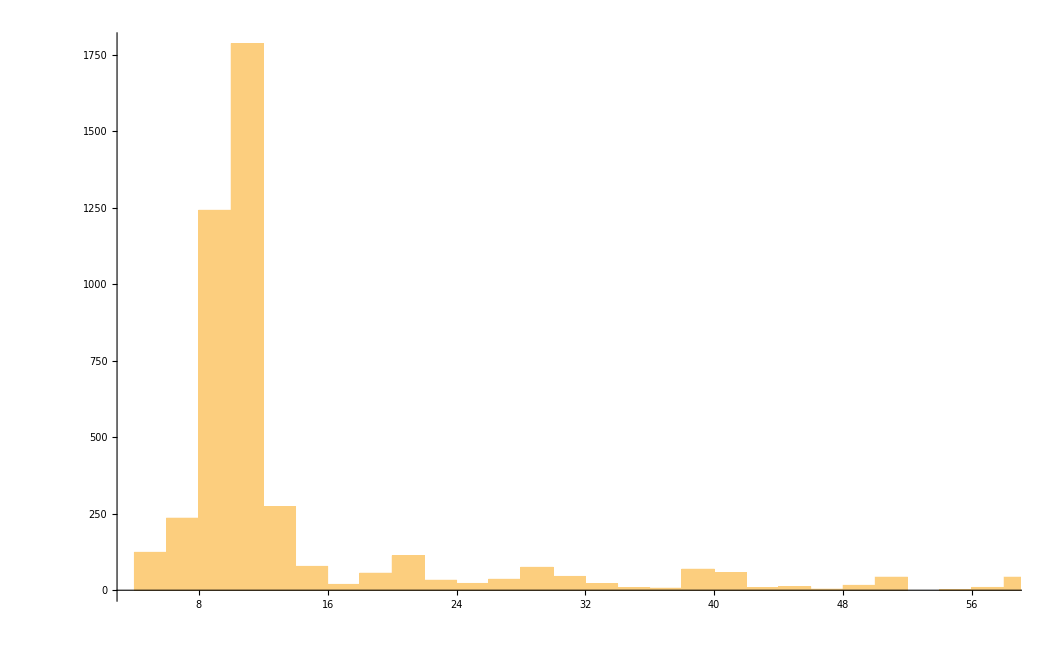

190.102

4.4375

```mathematica
L=Table[Q[[i,2]]-Q[[i-1,2]],{i,2,Length[Q]}];
Histogram[L]
Max[L]
Min[L]
```